{1.48438,Null}

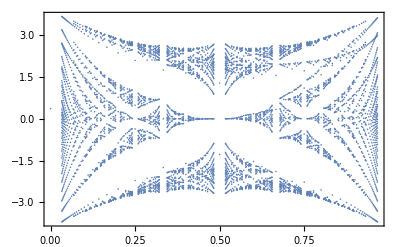

```mathematica
ϵ=0;
k1=0.5;
k2=0.5;
A[α_,c_,b_,q_]:=ϵ+2*Cos[k2*b+2*π*α]*Exp[-π 1/(2*q)]*LaguerreL[c,0,(π*1/q)]
B[a_,q_]:=Exp[ⅈ*k1*q*a]
B1[a_,q_]:=Exp[-ⅈ*k1*q*a]
ClearAll[matrix];
matrix[p_,q_,nu_:0]:=Module[{sigma},sigma=p/q;
N@SparseArray[{{m_,m_}->A[m*p/q,0,1,q],{i_,j_}/;Abs[i-j]==1&&i>j->B[1,q],{i_,j_}/;Abs[i-j]==1&&i<j->B1[1,q]},{q,q}]]

ClearAll[attachsigma]
attachsigma[sigma_,lst_]:={sigma,#}&/@lst

fracs=Table[p/q,{q,1,30},{p,0,q-1}]//Flatten//DeleteDuplicates;
pq={Numerator@#,Denominator@#}&/@fracs;
(ens=Eigenvalues[#]&/@(matrix[#[[1]],#[[2]]]&/@pq);)//Timing
pts=ListPlot[Flatten[#,1]&@MapThread[attachsigma,{fracs,ens}],Frame->True]
```

{0.10938,Null}

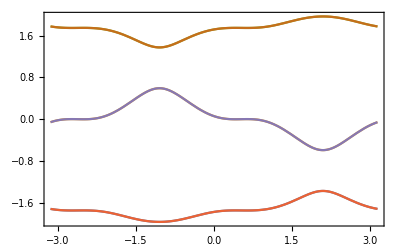

```mathematica
ϵ=0;
k1=0.5;
A[α_,c_,b_,q_]:=ϵ+2*Cos[k2*b+2*π*α]*Exp[-π 1/(2*q)]*LaguerreL[c,0,(π*1/q)]
B[a_,q_]:=Exp[ⅈ*k1*q*a]
B1[a_,q_]:=Exp[-ⅈ*k1*q*a]
ClearAll[matrix];
matrix[p_,q_,nu_:0]:=Module[{sigma},sigma=p/q;
N@SparseArray[{{m_,m_}->A[m*p/q,0,1,q],{i_,j_}/;Abs[i-j]==1&&i>j->B[1,q],{i_,j_}/;Abs[i-j]==1&&i<j->B1[1,q]},{q,q}]]

ClearAll[attachsigma]
attachsigma[sigma_,lst_]:={sigma,#}&/@lst
pq={{1,3},{1,3}};
(ens=Eigenvalues[#]&/@(matrix[#[[1]],#[[2]]]&/@pq);)//Timing
Plot[ens,{k2,-π,π},Frame->True]
```

```mathematica
ϵ=0;
k2=0.5;
A[α_,c_,b_,q_]:=ϵ+2*Cos[k2*b+2*π*α]*Exp[-π 1/(2*q)]*LaguerreL[c,0,(π*1/q)]
B[a_,q_]:=Exp[ⅈ*k1*q*a]
B1[a_,q_]:=Exp[-ⅈ*k1*q*a]
ClearAll[matrix];
matrix[p_,q_,nu_:0]:=Module[{sigma},sigma=p/q;
N@SparseArray[{{m_,m_}->A[m*p/q,0,1,q],{i_,j_}/;Abs[i-j]==1&&i>j->B[1,q],{i_,j_}/;Abs[i-j]==1&&i<j->B1[1,q]},{q,q}]]

ClearAll[attachsigma]
attachsigma[sigma_,lst_]:={sigma,#}&/@lst
pq={{1,3},{1,3}};
(ens=Eigenvalues[#]&/@(matrix[#[[1]],#[[2]]]&/@pq);)//Timing
Plot[ens,{k1,-π/3,π/3},Frame->True]
```

{0.0625,Null}

{0.10938,Null}

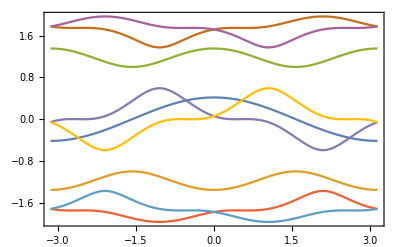

```mathematica
ϵ=0;
k1=0.5;
A[α_,c_,b_,q_]:=ϵ+2*Cos[k2*b+2*π*α]*Exp[-π 1/(2*q)]*LaguerreL[c,0,(π*1/q)]
B[a_,q_]:=Exp[ⅈ*k1*q*a]
B1[a_,q_]:=Exp[-ⅈ*k1*q*a]
ClearAll[matrix];
matrix[p_,q_,nu_:0]:=Module[{sigma},sigma=p/q;
N@SparseArray[{{m_,m_}->A[m*p/q,0,1,q],{i_,j_}/;Abs[i-j]==1&&i>j->B[1,q],{i_,j_}/;Abs[i-j]==1&&i<j->B1[1,q]},{q,q}]]

ClearAll[attachsigma]
attachsigma[sigma_,lst_]:={sigma,#}&/@lst

fracs=Table[p/q,{q,1,3},{p,0,q-1}]//Flatten//DeleteDuplicates;
pq={Numerator@#,Denominator@#}&/@fracs;
(ens=Eigenvalues[#]&/@(matrix[#[[1]],#[[2]]]&/@pq);)//Timing
Plot[ens,{k2,-π,π},Frame->True]
```